# Числено диференциране

## Табличната функция

съставяне на равномерна мрежа

```mathematica
a = 3.; b = 4;
n = 10;
h = (b-a)/n;
xt = Table[a+i*h, {i,0, n}]
```

{3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.}

```mathematica
f[x_]:=π Cos[2x-3]
yt = f[xt]
```

{-3.11015,-3.13624,-3.03729,-2.81725,-2.4849,-2.05348,-1.5402,-0.965515,-0.352338,0.274886,0.891151}

```mathematica
Length[xt]
```

11

## Намиране на производните с точност O(h) - първи порядък на грешката

### Първа производна

```mathematica
z = Table[(yt[[i+1]]-yt[[i]])/h,{i,1,n}]
```

{-0.260824,0.989494,2.20036,3.32351,4.31416,5.13282,5.74685,6.13177,6.27224,6.16265}

добавяме последния елемент

```mathematica
AppendTo[z,(yt[[n+1]]-yt[[n]])/h]
```

{-0.260824,0.989494,2.20036,3.32351,4.31416,5.13282,5.74685,6.13177,6.27224,6.16265,6.16265}

#### Оценка на грешката

теоретична грешка

```mathematica
h
```

0.1

истинската грешка

```mathematica
z (*приближени стойност*)
```

{-0.260824,0.989494,2.20036,3.32351,4.31416,5.13282,5.74685,6.13177,6.27224,6.16265,6.16265}

```mathematica
f'[xt](*точни стойност*)
```

{-0.886683,0.366776,1.60561,2.78044,3.84442,4.75513,5.47627,5.97909,6.24354,6.25909,6.0251}

```mathematica
Abs[z-f'[xt]]
```

{0.625859,0.622719,0.594752,0.543075,0.469747,0.377692,0.270579,0.152679,0.0286925,0.0964381,0.13755}

#### Визуализация на резултатите

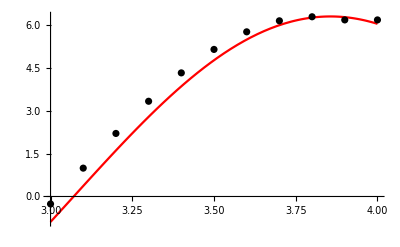

```mathematica
points = Table[{xt[[i]],z[[i]]},{i,1,n+1}];
grp = ListPlot[points, PlotStyle->Black];
grf = Plot[f'[x],{x,a,b}, PlotStyle->Red];
Show[grf, grp]
```

## Намиране на производните с точност O(h^2) - втори порядък на грешката

### Първа производна

попълваме вътрешните точки

```mathematica
z = Table[(yt[[i+1]]-yt[[i-1]])/(2h),{i,2,n}]
```

{0.364335,1.59493,2.76194,3.81884,4.72349,5.43984,5.93931,6.202,6.21744}

добавяме последния елемент

```mathematica
AppendTo[z,(yt[[n-1]]-4yt[[n]]+3yt[[n+1]])/(2h)]
```

{0.364335,1.59493,2.76194,3.81884,4.72349,5.43984,5.93931,6.202,6.21744,6.10785}

добавяме първия елемент

```mathematica
PrependTo[z,(-3yt[[1]]+4yt[[2]]-yt[[3]])/(2h)]
```

{-0.885983,0.364335,1.59493,2.76194,3.81884,4.72349,5.43984,5.93931,6.202,6.21744,6.10785}

#### Оценка на грешката

теоретична грешка

```mathematica
h^2
```

0.01

истинската грешка

```mathematica
z (*приближени стойност*)
```

{-0.885983,0.364335,1.59493,2.76194,3.81884,4.72349,5.43984,5.93931,6.202,6.21744,6.10785}

```mathematica
f'[xt](*точни стойност*)
```

{-0.886683,0.366776,1.60561,2.78044,3.84442,4.75513,5.47627,5.97909,6.24354,6.25909,6.0251}

```mathematica
Abs[z-f'[xt]]
```

{0.000700299,0.00244028,0.0106827,0.0184992,0.0255782,0.0316375,0.0364355,0.039781,0.0415405,0.0416439,0.0827556}

#### Визуализация на резултатите

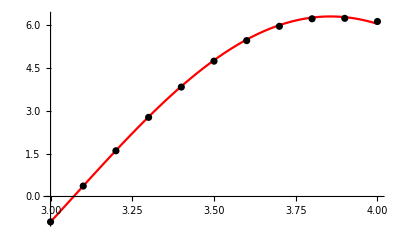

```mathematica
points = Table[{xt[[i]],z[[i]]},{i,1,n+1}];
grp = ListPlot[points, PlotStyle->Black];
grf = Plot[f'[x],{x,a,b}, PlotStyle->Red];
Show[grf, grp]
```

### Втора производна

попълваме вътрешните точки

```mathematica
z = Table[(yt[[i-1]]-2yt[[i]]+yt[[i+1]])/h^2,{i,2,n}]
```

{12.5032,12.1087,11.2315,9.90651,8.18658,6.14029,3.8492,1.40466,-1.09588}

добавяме последния елемент - SKIP

добавяме първия елемент - SKIP

#### Оценка на грешката

теоретична грешка

```mathematica
h^2
```

0.01

истинската грешка

```mathematica
z (*приближени стойност*)
```

{12.5032,12.1087,11.2315,9.90651,8.18658,6.14029,3.8492,1.40466,-1.09588}

```mathematica
f''[xt](*точни стойност*)
```

{12.4406,12.5449,12.1491,11.269,9.93959,8.21393,6.1608,3.86206,1.40935,-1.09954,-3.5646}

```mathematica
Table[Abs[z[[i]]-f''[xt[[i+1]]]],{i,1,n-1}]
```

{0.0417608,0.0404432,0.0375133,0.0330878,0.0273433,0.0205086,0.0128564,0.00469157,0.00366027}

#### Визуализация на резултатите

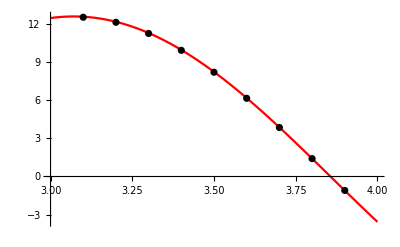

```mathematica
points = Table[{xt[[i+1]],z[[i]]},{i,1,n-1}];
grp = ListPlot[points, PlotStyle->Black];
grf = Plot[f''[x],{x,a,b}, PlotStyle->Red];
Show[grf, grp]
```

# Числено диференциране - увеличаваме точността чрез сгъстяване на мрежата

## Табличната функция

съставяне на равномерна мрежа

```mathematica
a = 3.; b = 4;
n = 100;
h = (b-a)/n;
xt = Table[a+i*h, {i,0, n}]
```

{3.,3.01,3.02,3.03,3.04,3.05,3.06,3.07,3.08,3.09,3.1,3.11,3.12,3.13,3.14,3.15,3.16,3.17,3.18,3.19,3.2,3.21,3.22,3.23,3.24,3.25,3.26,3.27,3.28,3.29,3.3,3.31,3.32,3.33,3.34,3.35,3.36,3.37,3.38,3.39,3.4,3.41,3.42,3.43,3.44,3.45,3.46,3.47,3.48,3.49,3.5,3.51,3.52,3.53,3.54,3.55,3.56,3.57,3.58,3.59,3.6,3.61,3.62,3.63,3.64,3.65,3.66,3.67,3.68,3.69,3.7,3.71,3.72,3.73,3.74,3.75,3.76,3.77,3.78,3.79,3.8,3.81,3.82,3.83,3.84,3.85,3.86,3.87,3.88,3.89,3.9,3.91,3.92,3.93,3.94,3.95,3.96,3.97,3.98,3.99,4.}

```mathematica
f[x_]:=π Cos[2x-3]
yt = f[xt]
```

{-3.11015,-3.1184,-3.12539,-3.13114,-3.13564,-3.13888,-3.14086,-3.14159,-3.14106,-3.13928,-3.13624,-3.13194,-3.12639,-3.1196,-3.11155,-3.10226,-3.09173,-3.07996,-3.06696,-3.05273,-3.03729,-3.02062,-3.00275,-2.98368,-2.96342,-2.94197,-2.91934,-2.89554,-2.87059,-2.84449,-2.81725,-2.78888,-2.7594,-2.72882,-2.69714,-2.66438,-2.63056,-2.59569,-2.55978,-2.52284,-2.4849,-2.44596,-2.40604,-2.36516,-2.32334,-2.28058,-2.23692,-2.19236,-2.14692,-2.10062,-2.05348,-2.00552,-1.95676,-1.90722,-1.85691,-1.80586,-1.75409,-1.70162,-1.64846,-1.59465,-1.5402,-1.48513,-1.42947,-1.37324,-1.31646,-1.25915,-1.20134,-1.14304,-1.08429,-1.02511,-0.965515,-0.905535,-0.845192,-0.784512,-0.723518,-0.662235,-0.600686,-0.538898,-0.476893,-0.414698,-0.352338,-0.289836,-0.227218,-0.16451,-0.101735,-0.0389201,0.0239105,0.0867316,0.149518,0.212244,0.274886,0.337418,0.399815,0.462051,0.524104,0.585946,0.647554,0.708903,0.769968,0.830726,0.891151}

```mathematica
Length[xt]
```

101

## Намиране на производните с точност O(h) - първи порядък на грешката

### Първа производна

```mathematica
z = Table[(yt[[i+1]]-yt[[i]])/h,{i,1,n}]
```

{-0.824423,-0.699691,-0.57468,-0.449438,-0.324017,-0.198466,-0.0728359,0.0528234,0.178462,0.304028,0.429474,0.554747,0.679799,0.804578,0.929036,1.05312,1.17679,1.29998,1.42266,1.54476,1.66625,1.78707,1.90718,2.02652,2.14505,2.26273,2.3795,2.49531,2.61013,2.72391,2.8366,2.94815,3.05852,3.16767,3.27555,3.38212,3.48734,3.59117,3.69355,3.79446,3.89386,3.99169,4.08793,4.18253,4.27546,4.36668,4.45616,4.54385,4.62972,4.71375,4.79588,4.8761,4.95437,5.03065,5.10493,5.17716,5.24732,5.31538,5.38132,5.4451,5.50671,5.56611,5.62329,5.67822,5.73087,5.78124,5.82929,5.87501,5.91838,5.95938,5.998,6.03422,6.06803,6.09941,6.12835,6.15484,6.17886,6.20042,6.21949,6.23608,6.25018,6.26177,6.27086,6.27744,6.28151,6.28306,6.28211,6.27864,6.27266,6.26417,6.25317,6.23968,6.22368,6.2052,6.18424,6.1608,6.1349,6.10655,6.07575,6.04252}

добавяме последния елемент

```mathematica
AppendTo[z,(yt[[n+1]]-yt[[n]])/h]
```

{-0.824423,-0.699691,-0.57468,-0.449438,-0.324017,-0.198466,-0.0728359,0.0528234,0.178462,0.304028,0.429474,0.554747,0.679799,0.804578,0.929036,1.05312,1.17679,1.29998,1.42266,1.54476,1.66625,1.78707,1.90718,2.02652,2.14505,2.26273,2.3795,2.49531,2.61013,2.72391,2.8366,2.94815,3.05852,3.16767,3.27555,3.38212,3.48734,3.59117,3.69355,3.79446,3.89386,3.99169,4.08793,4.18253,4.27546,4.36668,4.45616,4.54385,4.62972,4.71375,4.79588,4.8761,4.95437,5.03065,5.10493,5.17716,5.24732,5.31538,5.38132,5.4451,5.50671,5.56611,5.62329,5.67822,5.73087,5.78124,5.82929,5.87501,5.91838,5.95938,5.998,6.03422,6.06803,6.09941,6.12835,6.15484,6.17886,6.20042,6.21949,6.23608,6.25018,6.26177,6.27086,6.27744,6.28151,6.28306,6.28211,6.27864,6.27266,6.26417,6.25317,6.23968,6.22368,6.2052,6.18424,6.1608,6.1349,6.10655,6.07575,6.04252,6.04252}

#### Оценка на грешката

теоретична грешка

```mathematica
h
```

0.01

истинската грешка

```mathematica
z (*приближени стойност*)
```

{-0.824423,-0.699691,-0.57468,-0.449438,-0.324017,-0.198466,-0.0728359,0.0528234,0.178462,0.304028,0.429474,0.554747,0.679799,0.804578,0.929036,1.05312,1.17679,1.29998,1.42266,1.54476,1.66625,1.78707,1.90718,2.02652,2.14505,2.26273,2.3795,2.49531,2.61013,2.72391,2.8366,2.94815,3.05852,3.16767,3.27555,3.38212,3.48734,3.59117,3.69355,3.79446,3.89386,3.99169,4.08793,4.18253,4.27546,4.36668,4.45616,4.54385,4.62972,4.71375,4.79588,4.8761,4.95437,5.03065,5.10493,5.17716,5.24732,5.31538,5.38132,5.4451,5.50671,5.56611,5.62329,5.67822,5.73087,5.78124,5.82929,5.87501,5.91838,5.95938,5.998,6.03422,6.06803,6.09941,6.12835,6.15484,6.17886,6.20042,6.21949,6.23608,6.25018,6.26177,6.27086,6.27744,6.28151,6.28306,6.28211,6.27864,6.27266,6.26417,6.25317,6.23968,6.22368,6.2052,6.18424,6.1608,6.1349,6.10655,6.07575,6.04252,6.04252}

```mathematica
f'[xt](*точни стойност*)
```

{-0.886683,-0.762108,-0.637228,-0.512093,-0.386753,-0.261259,-0.13566,-0.0100069,0.11565,0.241261,0.366776,0.492143,0.617314,0.742238,0.866865,0.991145,1.11503,1.23847,1.36141,1.48381,1.60561,1.72677,1.84725,1.96698,2.08592,2.20404,2.32127,2.43757,2.55289,2.6672,2.78044,2.89256,3.00353,3.1133,3.22182,3.32906,3.43496,3.53949,3.6426,3.74426,3.84442,3.94304,4.04008,4.13551,4.22928,4.32136,4.41172,4.5003,4.58709,4.67205,4.75513,4.83631,4.91556,4.99284,5.06813,5.14139,5.21259,5.2817,5.34871,5.41357,5.47627,5.53678,5.59507,5.65113,5.70493,5.75644,5.80565,5.85254,5.89709,5.93928,5.97909,6.01651,6.05153,6.08413,6.11429,6.142,6.16726,6.19005,6.21037,6.2282,6.24354,6.25639,6.26673,6.27456,6.27989,6.2827,6.283,6.28079,6.27607,6.26883,6.25909,6.24684,6.2321,6.21486,6.19513,6.17293,6.14826,6.12113,6.09155,6.05954,6.0251}

```mathematica
Abs[z-f'[xt]]
```

{0.0622601,0.0624167,0.0625483,0.0626549,0.0627364,0.0627928,0.0628242,0.0628303,0.0628114,0.0627673,0.0626982,0.0626039,0.0624846,0.0623403,0.0621711,0.061977,0.0617582,0.0615146,0.0612464,0.0609537,0.0606367,0.0602953,0.0599299,0.0595405,0.0591273,0.0586904,0.0582301,0.0577464,0.0572397,0.0567101,0.0561578,0.055583,0.054986,0.054367,0.0537262,0.053064,0.0523805,0.0516761,0.050951,0.0502056,0.04944,0.0486547,0.0478499,0.047026,0.0461833,0.0453221,0.0444427,0.0435456,0.0426311,0.0416995,0.0407513,0.0397867,0.0388062,0.0378102,0.0367991,0.0357733,0.0347332,0.0336791,0.0326116,0.0315311,0.0304379,0.0293326,0.0282155,0.0270871,0.0259479,0.0247984,0.0236389,0.0224699,0.021292,0.0201055,0.0189111,0.017709,0.0164999,0.0152841,0.0140623,0.0128348,0.0116022,0.0103649,0.00912353,0.00787849,0.00663029,0.00537944,0.00412644,0.00287179,0.00161599,0.000359538,0.000897052,0.00215328,0.00340865,0.00466266,0.0059148,0.00716458,0.00841149,0.00965504,0.0108947,0.01213,0.0133605,0.0145857,0.0158049,0.0170179,0.0174208}

#### Визуализация на резултатите

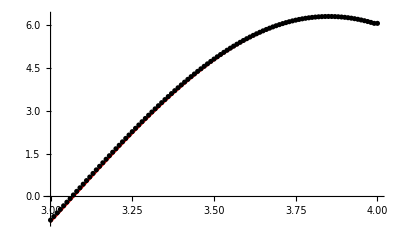

```mathematica
points = Table[{xt[[i]],z[[i]]},{i,1,n+1}];
grp = ListPlot[points, PlotStyle->Black];
grf = Plot[f'[x],{x,a,b}, PlotStyle->Red];
Show[grf, grp]
```

## Намиране на производните с точност O(h^2) - втори порядък на грешката

### Първа производна

попълваме вътрешните точки

```mathematica
z = Table[(yt[[i+1]]-yt[[i-1]])/(2h),{i,2,n}]
```

{-0.762057,-0.637186,-0.512059,-0.386728,-0.261242,-0.135651,-0.0100063,0.115643,0.241245,0.366751,0.49211,0.617273,0.742189,0.866807,0.991079,1.11495,1.23838,1.36132,1.48371,1.60551,1.72666,1.84712,1.96685,2.08579,2.20389,2.32111,2.43741,2.55272,2.66702,2.78025,2.89237,3.00333,3.11309,3.22161,3.32884,3.43473,3.53925,3.64236,3.74401,3.84416,3.94277,4.03981,4.13523,4.229,4.32107,4.41142,4.5,4.58679,4.67173,4.75481,4.83599,4.91523,4.99251,5.06779,5.14104,5.21224,5.28135,5.34835,5.41321,5.47591,5.53641,5.5947,5.65075,5.70455,5.75606,5.80526,5.85215,5.8967,5.93888,5.97869,6.01611,6.05113,6.08372,6.11388,6.14159,6.16685,6.18964,6.20996,6.22779,6.24313,6.25597,6.26631,6.27415,6.27947,6.28228,6.28258,6.28037,6.27565,6.26841,6.25867,6.24642,6.23168,6.21444,6.19472,6.17252,6.14785,6.12072,6.09115,6.05913}

добавяме последния елемент

```mathematica
AppendTo[z,(yt[[n-1]]-4yt[[n]]+3yt[[n+1]])/(2h)]
```

{-0.762057,-0.637186,-0.512059,-0.386728,-0.261242,-0.135651,-0.0100063,0.115643,0.241245,0.366751,0.49211,0.617273,0.742189,0.866807,0.991079,1.11495,1.23838,1.36132,1.48371,1.60551,1.72666,1.84712,1.96685,2.08579,2.20389,2.32111,2.43741,2.55272,2.66702,2.78025,2.89237,3.00333,3.11309,3.22161,3.32884,3.43473,3.53925,3.64236,3.74401,3.84416,3.94277,4.03981,4.13523,4.229,4.32107,4.41142,4.5,4.58679,4.67173,4.75481,4.83599,4.91523,4.99251,5.06779,5.14104,5.21224,5.28135,5.34835,5.41321,5.47591,5.53641,5.5947,5.65075,5.70455,5.75606,5.80526,5.85215,5.8967,5.93888,5.97869,6.01611,6.05113,6.08372,6.11388,6.14159,6.16685,6.18964,6.20996,6.22779,6.24313,6.25597,6.26631,6.27415,6.27947,6.28228,6.28258,6.28037,6.27565,6.26841,6.25867,6.24642,6.23168,6.21444,6.19472,6.17252,6.14785,6.12072,6.09115,6.05913,6.02591}

добавяме първия елемент

```mathematica
PrependTo[z,(-3yt[[1]]+4yt[[2]]-yt[[3]])/(2h)]
```

{-0.886789,-0.762057,-0.637186,-0.512059,-0.386728,-0.261242,-0.135651,-0.0100063,0.115643,0.241245,0.366751,0.49211,0.617273,0.742189,0.866807,0.991079,1.11495,1.23838,1.36132,1.48371,1.60551,1.72666,1.84712,1.96685,2.08579,2.20389,2.32111,2.43741,2.55272,2.66702,2.78025,2.89237,3.00333,3.11309,3.22161,3.32884,3.43473,3.53925,3.64236,3.74401,3.84416,3.94277,4.03981,4.13523,4.229,4.32107,4.41142,4.5,4.58679,4.67173,4.75481,4.83599,4.91523,4.99251,5.06779,5.14104,5.21224,5.28135,5.34835,5.41321,5.47591,5.53641,5.5947,5.65075,5.70455,5.75606,5.80526,5.85215,5.8967,5.93888,5.97869,6.01611,6.05113,6.08372,6.11388,6.14159,6.16685,6.18964,6.20996,6.22779,6.24313,6.25597,6.26631,6.27415,6.27947,6.28228,6.28258,6.28037,6.27565,6.26841,6.25867,6.24642,6.23168,6.21444,6.19472,6.17252,6.14785,6.12072,6.09115,6.05913,6.02591}

#### Оценка на грешката

теоретична грешка

```mathematica
h^2
```

0.0001

истинската грешка

```mathematica
z (*приближени стойност*)
```

{-0.886789,-0.762057,-0.637186,-0.512059,-0.386728,-0.261242,-0.135651,-0.0100063,0.115643,0.241245,0.366751,0.49211,0.617273,0.742189,0.866807,0.991079,1.11495,1.23838,1.36132,1.48371,1.60551,1.72666,1.84712,1.96685,2.08579,2.20389,2.32111,2.43741,2.55272,2.66702,2.78025,2.89237,3.00333,3.11309,3.22161,3.32884,3.43473,3.53925,3.64236,3.74401,3.84416,3.94277,4.03981,4.13523,4.229,4.32107,4.41142,4.5,4.58679,4.67173,4.75481,4.83599,4.91523,4.99251,5.06779,5.14104,5.21224,5.28135,5.34835,5.41321,5.47591,5.53641,5.5947,5.65075,5.70455,5.75606,5.80526,5.85215,5.8967,5.93888,5.97869,6.01611,6.05113,6.08372,6.11388,6.14159,6.16685,6.18964,6.20996,6.22779,6.24313,6.25597,6.26631,6.27415,6.27947,6.28228,6.28258,6.28037,6.27565,6.26841,6.25867,6.24642,6.23168,6.21444,6.19472,6.17252,6.14785,6.12072,6.09115,6.05913,6.02591}

```mathematica
f'[xt](*точни стойност*)
```

{-0.886683,-0.762108,-0.637228,-0.512093,-0.386753,-0.261259,-0.13566,-0.0100069,0.11565,0.241261,0.366776,0.492143,0.617314,0.742238,0.866865,0.991145,1.11503,1.23847,1.36141,1.48381,1.60561,1.72677,1.84725,1.96698,2.08592,2.20404,2.32127,2.43757,2.55289,2.6672,2.78044,2.89256,3.00353,3.1133,3.22182,3.32906,3.43496,3.53949,3.6426,3.74426,3.84442,3.94304,4.04008,4.13551,4.22928,4.32136,4.41172,4.5003,4.58709,4.67205,4.75513,4.83631,4.91556,4.99284,5.06813,5.14139,5.21259,5.2817,5.34871,5.41357,5.47627,5.53678,5.59507,5.65113,5.70493,5.75644,5.80565,5.85254,5.89709,5.93928,5.97909,6.01651,6.05153,6.08413,6.11429,6.142,6.16726,6.19005,6.21037,6.2282,6.24354,6.25639,6.26673,6.27456,6.27989,6.2827,6.283,6.28079,6.27607,6.26883,6.25909,6.24684,6.2321,6.21486,6.19513,6.17293,6.14826,6.12113,6.09155,6.05954,6.0251}

```mathematica
Abs[z-f'[xt]]
```

{0.000105768,0.0000508062,0.000042481,0.0000341389,0.000025783,0.0000174169,9.04383×10^-6,6.67116×10^-7,7.70986×10^-6,0.0000160838,0.0000244512,0.0000328089,0.0000411535,0.0000494815,0.0000577899,0.000066075,0.0000743338,0.0000825628,0.0000907588,0.0000989185,0.000107039,0.000115116,0.000123147,0.000131129,0.000139059,0.000146933,0.000154748,0.000162501,0.00017019,0.00017781,0.000185359,0.000192834,0.000200232,0.000207549,0.000214784,0.000221933,0.000228993,0.000235961,0.000242835,0.000249612,0.000256289,0.000262864,0.000269333,0.000275695,0.000281946,0.000288085,0.000294108,0.000300014,0.0003058,0.000311463,0.000317002,0.000322414,0.000327698,0.00033285,0.000337868,0.000342752,0.000347499,0.000352107,0.000356573,0.000360898,0.000365078,0.000369111,0.000372998,0.000376735,0.000380321,0.000383755,0.000387036,0.000390162,0.000393131,0.000395944,0.000398598,0.000401093,0.000403427,0.0004056,0.000407611,0.000409459,0.000411143,0.000412662,0.000414016,0.000415205,0.000416228,0.000417084,0.000417774,0.000418296,0.000418651,0.000418838,0.000418859,0.000418711,0.000418396,0.000417914,0.000417264,0.000416448,0.000415465,0.000414316,0.000413001,0.000411521,0.000409876,0.000408067,0.000406095,0.000403961,0.000806798}

#### Визуализация на резултатите

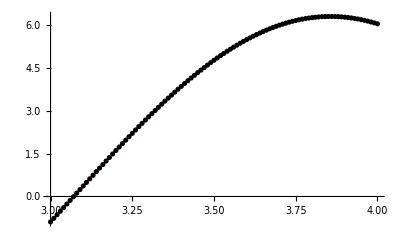

```mathematica
points = Table[{xt[[i]],z[[i]]},{i,1,n+1}];
grp = ListPlot[points, PlotStyle->Black];
grf = Plot[f'[x],{x,a,b}, PlotStyle->Red];
Show[grf, grp]
```

### Втора производна

попълваме вътрешните точки

```mathematica
z = Table[(yt[[i-1]]-2yt[[i]]+yt[[i+1]])/h^2,{i,2,n}]
```

{12.4732,12.5012,12.5241,12.5421,12.5551,12.563,12.5659,12.5638,12.5567,12.5445,12.5273,12.5052,12.478,12.4458,12.4086,12.3665,12.3194,12.2674,12.2105,12.1487,12.0821,12.0106,11.9343,11.8533,11.7675,11.677,11.5818,11.482,11.3776,11.2686,11.1552,11.0372,10.9149,10.7882,10.6572,10.5219,10.3824,10.2388,10.091,9.93926,9.78351,9.62385,9.46034,9.29304,9.12203,8.94737,8.76913,8.58738,8.4022,8.21365,8.02183,7.82679,7.62862,7.4274,7.22321,7.01613,6.80624,6.59364,6.37839,6.16059,5.94033,5.7177,5.49277,5.26565,5.03642,4.80518,4.57202,4.33702,4.1003,3.86193,3.62202,3.38066,3.13794,2.89398,2.64885,2.40266,2.15552,1.90751,1.65874,1.4093,1.1593,0.908842,0.658016,0.406927,0.155675,-0.0956388,-0.346915,-0.598052,-0.84895,-1.09951,-1.34963,-1.59921,-1.84814,-2.09634,-2.34371,-2.59013,-2.83552,-3.07977,-3.32279}

добавяме последния елемент - SKIP

добавяме първия елемент - SKIP

#### Оценка на грешката

теоретична грешка

```mathematica
h^2
```

0.0001

истинската грешка

```mathematica
z (*приближени стойност*)
```

{12.4732,12.5012,12.5241,12.5421,12.5551,12.563,12.5659,12.5638,12.5567,12.5445,12.5273,12.5052,12.478,12.4458,12.4086,12.3665,12.3194,12.2674,12.2105,12.1487,12.0821,12.0106,11.9343,11.8533,11.7675,11.677,11.5818,11.482,11.3776,11.2686,11.1552,11.0372,10.9149,10.7882,10.6572,10.5219,10.3824,10.2388,10.091,9.93926,9.78351,9.62385,9.46034,9.29304,9.12203,8.94737,8.76913,8.58738,8.4022,8.21365,8.02183,7.82679,7.62862,7.4274,7.22321,7.01613,6.80624,6.59364,6.37839,6.16059,5.94033,5.7177,5.49277,5.26565,5.03642,4.80518,4.57202,4.33702,4.1003,3.86193,3.62202,3.38066,3.13794,2.89398,2.64885,2.40266,2.15552,1.90751,1.65874,1.4093,1.1593,0.908842,0.658016,0.406927,0.155675,-0.0956388,-0.346915,-0.598052,-0.84895,-1.09951,-1.34963,-1.59921,-1.84814,-2.09634,-2.34371,-2.59013,-2.83552,-3.07977,-3.32279}

```mathematica
f''[xt](*точни стойност*)
```

{12.4406,12.4736,12.5016,12.5246,12.5425,12.5555,12.5634,12.5664,12.5642,12.5571,12.5449,12.5278,12.5056,12.4784,12.4462,12.409,12.3669,12.3198,12.2678,12.2109,12.1491,12.0825,12.011,11.9347,11.8537,11.7679,11.6774,11.5822,11.4824,11.378,11.269,11.1555,11.0376,10.9153,10.7886,10.6575,10.5223,10.3828,10.2391,10.0914,9.93959,9.78384,9.62417,9.46065,9.29335,9.12233,8.94767,8.76942,8.58767,8.40248,8.21393,8.02209,7.82705,7.62887,7.42765,7.22345,7.01636,6.80647,6.59386,6.3786,6.1608,5.94053,5.71789,5.49295,5.26583,5.03659,4.80534,4.57217,4.33717,4.10043,3.86206,3.62214,3.38077,3.13805,2.89407,2.64894,2.40274,2.15559,1.90757,1.65879,1.40935,1.15934,0.908872,0.658038,0.406941,0.155681,-0.095642,-0.346926,-0.598072,-0.848978,-1.09954,-1.34967,-1.59926,-1.84821,-2.09641,-2.34378,-2.59022,-2.83561,-3.07987,-3.3229,-3.5646}

```mathematica
Table[Abs[z[[i]]-f''[xt[[i+1]]]],{i,1,n-1}]
```

{0.000415781,0.000416714,0.00041748,0.000418079,0.000418511,0.000418776,0.000418873,0.000418802,0.000418565,0.000418159,0.000417587,0.000416847,0.00041594,0.000414868,0.000413629,0.000412225,0.000410656,0.000408923,0.000407026,0.000404966,0.000402744,0.000400362,0.000397819,0.000395117,0.000392257,0.00038924,0.000386067,0.00038274,0.00037926,0.000375628,0.000371846,0.000367915,0.000363837,0.000359614,0.000355247,0.000350737,0.000346087,0.000341299,0.000336375,0.000331315,0.000326124,0.000320801,0.000315351,0.000309774,0.000304074,0.000298252,0.00029231,0.000286252,0.000280079,0.000273794,0.0002674,0.000260898,0.000254292,0.000247585,0.000240778,0.000233876,0.000226879,0.000219792,0.000212617,0.000205357,0.000198015,0.000190594,0.000183096,0.000175525,0.000167884,0.000160176,0.000152404,0.00014457,0.000136679,0.000128734,0.000120736,0.000112691,0.0001046,0.0000964678,0.0000882968,0.0000800904,0.000071852,0.000063585,0.0000552924,0.0000469777,0.0000386443,0.0000302954,0.0000219343,0.0000135645,5.18931×10^-6,3.18805×10^-6,0.000011564,0.0000199355,0.0000282989,0.000036651,0.0000449884,0.0000533079,0.000061606,0.0000698796,0.000078125,0.0000863394,0.0000945192,0.000102661,0.000110762}

#### Визуализация на резултатите

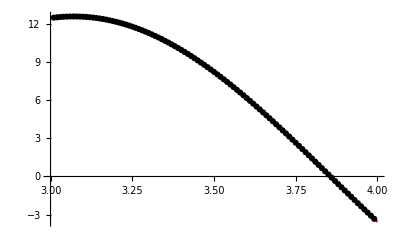

```mathematica
points = Table[{xt[[i+1]],z[[i]]},{i,1,n-1}];
grp = ListPlot[points, PlotStyle->Black];
grf = Plot[f''[x],{x,a,b}, PlotStyle->Red];
Show[grf, grp]
```